This script is a part of ANGEL project.
V 1.0.0
2017.11.29
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Clearing all variables *)
Needs["JLink`"];(* Not to be any problems with exporting *)
ReinstallJava[JVMArguments -> "-Xmx512m"];(* DO NOT TOUCH! *)
```

```mathematica
Kprt=-131.85; (* Kprt for current resonance *)
```

```mathematica
importDir = "";(* Directory for importing data *)
exportDir = "";(* Directory for exporting data *)
```

```mathematica
lorenz[y0_,A_,μ_, σ_, x_]:=y0 + (2A)/π×σ/(4 (x-μ)^2+σ^2);(* Lorenz function *)
lorenzInverse[y0_,A_,μ_, σ_, y_,sgn_]:=Sign[sgn]×√((2 A σ)/(4 π (y-y0))-σ^2/4)+μ;(* Inverse Lorenz function *)
paraboloid[y0_,A_,μ_,x_] := y0 + A(x-μ)^2;(* Paraboloid *)
```

```mathematica
Experiments = Length[FileNames["PreScan*.dat",FileNameJoin[{NotebookDirectory[ ],importDir}]]]; (* Getting experiments ammount *)
(* Preparing tables for plotting and exporting *)
TemperatureLorenzKineticsPlotRaw=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsPlotAFix=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsPlotY0Fix=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsExport=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsPlotAllFixDelta=Table[{i},{i,1,Experiments}];
```

```mathematica
PreScanData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"PreScan.dat"}]][[2;;]];(* Importing rezonance profile *)
```

```mathematica
PreScanFrequency=PreScanData[[All,1]];(* Getting frequency column *)
PreScanTheta=PreScanData[[All,6]];(* Getting phase column *)
PreScanData=Transpose[{PreScanFrequency,PreScanTheta}];(* Forming prescan data *)
```

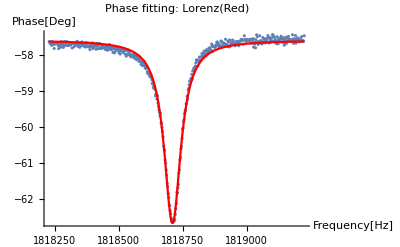

```mathematica
PreScanLorenzFit=NonlinearModelFit[(* Fitting prescan data with lorenz *)
PreScanData,lorenz[y0,A,μ, σ,x],
{{y0,Max[PreScanTheta]},
{A,Min[PreScanTheta]-Max[PreScanTheta]},
{μ,PreScanFrequency[[Position[PreScanTheta,Min[PreScanTheta]][[1,1]]]]},
{σ,10}},
x];
parametersTablePreScanLorenzFit=PreScanLorenzFit["ParameterTable"];(* Getting fited parameters and their errors *)
y0LorenzFit=parametersTablePreScanLorenzFit[[1,1,2,2]];δy0LorenzFit=parametersTablePreScanLorenzFit[[1,1,2,3]];
ALorenzFit=parametersTablePreScanLorenzFit[[1,1,3,2]];δALorenzFit=parametersTablePreScanLorenzFit[[1,1,3,3]];
μLorenzFit=parametersTablePreScanLorenzFit[[1,1,4,2]];δμLorenzFit=parametersTablePreScanLorenzFit[[1,1,4,3]];
σLorenzFit=parametersTablePreScanLorenzFit[[1,1,5,2]];δσLorenzFit=parametersTablePreScanLorenzFit[[1,1,5,3]];
PreScanFitPlot=Show[(* Plotting round data and fittings *)
ListPlot[PreScanData,PlotLabel->"Phase fitting: Lorenz(Red)",AxesLabel->{"Frequency[Hz]","Phase[Deg]"},PlotRange->All],
Plot[lorenz[y0LorenzFit,ALorenzFit,μLorenzFit, σLorenzFit,x],{x,Min[PreScanFrequency],Max[PreScanFrequency]},ColorFunction->Function[{x,y},Red],PlotRange->All]
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"PreScanData_Fit.png"}],PreScanFitPlot];(* Exporting plot from above *)
```

```mathematica
KineticsData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"Kinetic_Round_1.dat"}]][[2;;]];(* Importing kinetics data *)
KineticsTime=KineticsData[[All,1]];(* Getting time column *)
KineticsTheta=KineticsData[[All,4]];(* Getting phase column *)
KineticsData=Transpose[{KineticsTime,KineticsTheta}];(* Forming kinetics data *)
```

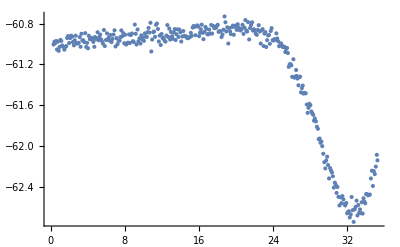

```mathematica
ListPlot[KineticsData]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"KineticsData_Raw.png"}],
ListPlot[KineticsData,PlotLabel->"Kinetics Data ",AxesLabel->{"Time[s]","Phase[deg]"},ImageSize->Medium,PlotRange->All]];
```

```mathematica
(* Forming data for kinetics fit *)
TimeMinTheta=KineticsTime[[Position[KineticsTheta,Min[KineticsTheta]][[1,1]]]];(* Finding phase minimum *)
TemperatureLorenzFromTimeRaw=Table[{KineticsTime[[i]],Re[lorenzInverse[y0LorenzFit,ALorenzFit,μLorenzFit, σLorenzFit,KineticsTheta[[i]],-KineticsTime[[i]]+TimeMinTheta]]},
{i,1,Length[KineticsTime]}];(* Frequency -> ΔTemperature *)
```

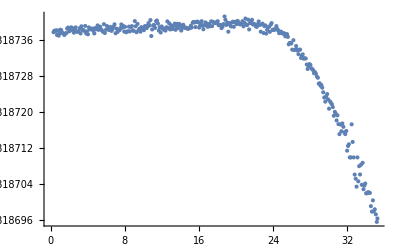

```mathematica
ListPlot[TemperatureLorenzFromTimeRaw]
```

```mathematica
TemperatureLorenzFromTimeRaw[[All,2]]=(TemperatureLorenzFromTimeRaw[[All,2]]-TemperatureLorenzFromTimeRaw[[1,2]])/Kprt;(* Forming data for plotting and exporting *)
```

```mathematica
TemperatureLorenzKineticsPlotRaw=TemperatureLorenzFromTimeRaw;
```

```mathematica
TemperatureLorenzKineticsExport=Prepend[TemperatureLorenzFromTimeRaw,{"Time[s] Lorenz Raw","ΔTemperature[C]"}];
```

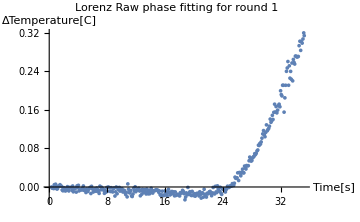

```mathematica
(* Plotting round kinetics data *)
TemperatureLorenzKineticsPlotRound= ListPlot[Evaluate[{TemperatureLorenzFromTimeRaw}],
PlotLabel->"Lorenz Raw phase fitting for round 1",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All]
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"KineticsRound 1"<>".png"}],TemperatureLorenzKineticsPlotRound];
```

```mathematica
TemperatureData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"Temperature.dat"}]][[2;;]];
TemperatureData[[All,2]]=TemperatureData[[All,2]]-TemperatureData[[1,2]];
```

```mathematica
SlowData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"Kinetic.dat"}]][[2;;]];
SlowData=Transpose[{SlowData[[All,1]],(SlowData[[All,3]]-μLorenzFit)/Kprt}];
```

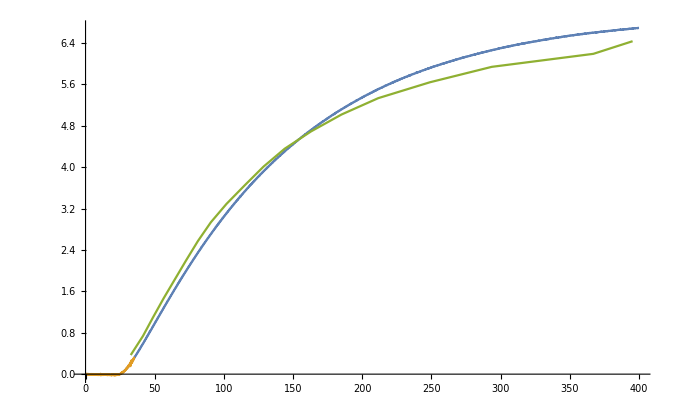

```mathematica
ListPlot[Evaluate[{TemperatureData,TemperatureLorenzFromTimeRaw,SlowData}],Joined->{True,True,True}]
```

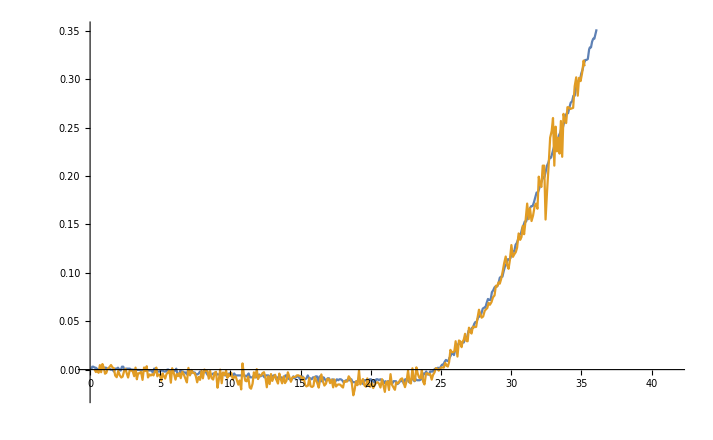

```mathematica
ListPlot[Evaluate[{TemperatureData[[;;400]],TemperatureLorenzFromTimeRaw,SlowData[[;;2]]}],Joined->{True,True,True}]
```

```mathematica
i1 = Interpolation[TemperatureLorenzFromTimeRaw];
```

```mathematica
i2 = Interpolation[TemperatureData[[;;400]]];
```

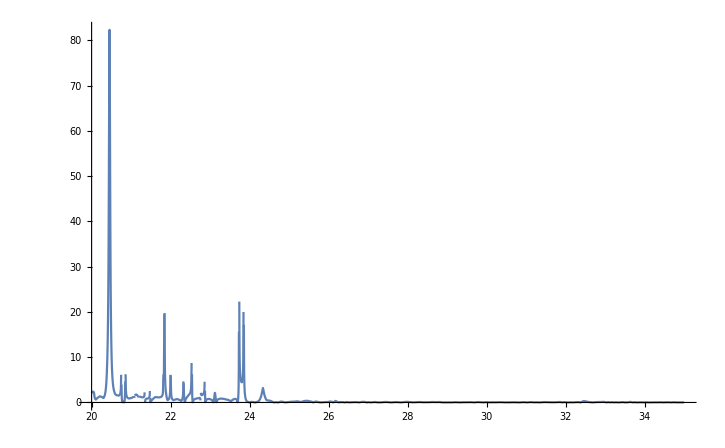

```mathematica
Plot[{(*i1[x],i2[x],*)Abs[i1[x]-i2[x]]}/Abs[i1[x]-i1[22]],{x,20,35},PlotRange->All]
```